```mathematica
AnDn-04
10 - elementov //bruteforce
```

```mathematica
Podatki in izračun koeficienta torzijske vzmeti
```

```mathematica
n=10;
m=282 4/n;  (*masa posameznega elementa se primerno zmanjša*)
L=0.74 4/n;
d=3940;
vstr=1.9 10^-06;
modul=2.1 10^11;
g=9.81;
k=modul vstr/L;
J1=1/3m L^2;
J2=J1/4;
```

```mathematica
Določitev vektorjev, izračun hitrosti,energijska funkcija
```

```mathematica
rt1={L/2 Cos[ϕ1[t]],-L/2 Sin[ϕ1[t]]};
rt2={L Cos[ϕ1[t]]+L/2 Cos[ϕ2[t]],-L Sin[ϕ1[t]]-L/2 Sin[ϕ2[t]]};
rt3={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L/2 Cos[ϕ3[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L/2 Sin[ϕ3[t]]};
rt4={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L/2 Cos[ϕ4[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L/2 Sin[ϕ4[t]]};rt5={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L Cos[ϕ4[t]]+L/2 Cos[ϕ5[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L Sin[ϕ4[t]]-L/2 Sin[ϕ5[t]]};
rt6={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L Cos[ϕ4[t]]+L Cos[ϕ5[t]]+L/2 Cos[ϕ6[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L Sin[ϕ4[t]]-L Sin[ϕ5[t]]+L/2 Sin[ϕ6[t]]};
rt7={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L Cos[ϕ4[t]]+L Cos[ϕ5[t]]+L Cos[ϕ6[t]]+L/2 Cos[ϕ7[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L Sin[ϕ4[t]]-L Sin[ϕ5[t]]+L Sin[ϕ6[t]]+L/2 Sin[ϕ7[t]]};
rt8={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L Cos[ϕ4[t]]+L Cos[ϕ5[t]]+L Cos[ϕ6[t]]+L Cos[ϕ7[t]]+L/2 Cos[ϕ8[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L Sin[ϕ4[t]]-L Sin[ϕ5[t]]+L Sin[ϕ6[t]]+L Sin[ϕ7[t]]+L/2 Sin[ϕ8[t]]};
rt9={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L Cos[ϕ4[t]]+L Cos[ϕ5[t]]+L Cos[ϕ6[t]]+L Cos[ϕ7[t]]+L Cos[ϕ8[t]]+L/2 Cos[ϕ9[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L Sin[ϕ4[t]]-L Sin[ϕ5[t]]+L Sin[ϕ6[t]]+L Sin[ϕ7[t]]+L Sin[ϕ8[t]]+L/2 Sin[ϕ9[t]]};
rt10={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L Cos[ϕ4[t]]+L Cos[ϕ5[t]]+L Cos[ϕ6[t]]+L Cos[ϕ7[t]]+L Cos[ϕ8[t]]+L Cos[ϕ9[t]]+L/2 Cos[ϕ10[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L Sin[ϕ4[t]]-L Sin[ϕ5[t]]+L Sin[ϕ6[t]]+L Sin[ϕ7[t]]+L Sin[ϕ8[t]]+L Sin[ϕ9[t]]+L/2 Sin[ϕ10[t]]};

vt2=D[rt2,t];
vt3=D[rt3,t];
vt4=D[rt4,t];
vt5=D[rt5,t];
vt6=D[rt6,t];
vt7=D[rt7,t];
vt8=D[rt8,t];
vt9=D[rt9,t];
vt10=D[rt10,t];
Ek[t_]=1/2 (ϕ1'[t])^2 J1+1/2 m vt2.vt2+1/2 (ϕ2'[t])^2 J2+1/2 m vt3.vt3+1/2 (ϕ3'[t])^2 J2+1/2 m vt4.vt4+1/2 (ϕ4'[t])^2 J2+1/2 m vt5.vt5+1/2 (ϕ5'[t])^2 J2+1/2 m vt6.vt6+1/2 (ϕ6'[t])^2 J2+1/2 m vt7.vt7+1/2 (ϕ7'[t])^2 J2+1/2 m vt8.vt8+1/2 (ϕ8'[t])^2 J2+1/2 m vt9.vt9+1/2 (ϕ9'[t])^2 J2+1/2 m vt10.vt10+1/2 (ϕ10'[t])^2 J1;
Ep[t_]=1/2 k (ϕ1[t]-ϕ2[t])^2+1/2 k (ϕ2[t]-ϕ3[t])^2+1/2 k (ϕ3[t]-ϕ4[t])^2+1/2 k (ϕ4[t]-ϕ5[t])^2+1/2 k (ϕ5[t]+ϕ6[t])^2+1/2 k (ϕ7[t]-ϕ6[t])^2+1/2 k (ϕ8[t]-ϕ7[t])^2+1/2 k (ϕ9[t]-ϕ8[t])^2+1/2 k (ϕ10[t]-ϕ9[t])^2+m g (rt1[[2]]+rt2[[2]]+rt3[[2]]+rt4[[2]]+rt5[[2]]+rt6[[2]]+rt7[[2]]+rt8[[2]]+rt9[[2]]+rt10[[2]]);
La[t_]=Ek[t]-Ep[t];
```

```mathematica
Določitev posplošenih sil
```

```mathematica
rA={L Cos[ϕ1[t]]+L Cos[ϕ2[t]]+L Cos[ϕ3[t]]+L Cos[ϕ4[t]]+L Cos[ϕ5[t]],-L Sin[ϕ1[t]]-L Sin[ϕ2[t]]-L Sin[ϕ3[t]]-L Sin[ϕ4[t]]-L Sin[ϕ5[t]]};
vA=D[rA,t];
drA1=D[rA,ϕ1[t]];
drA2=D[rA,ϕ2[t]];
drA3=D[rA,ϕ3[t]];
drA4=D[rA,ϕ4[t]];
drA5=D[rA,ϕ5[t]];
F={0,-d vA[[2]]};
Q1[t_]=F.drA1;
Q2[t_]=F.drA2;
Q3[t_]=F.drA3;
Q4[t_]=F.drA4;
Q5[t_]=F.drA5;
```

```mathematica
Gibalne enačbe
```

```mathematica
ddL1[t_]=D[D[La[t],ϕ1'[t]],t]; (*po koordinati' in času*)
ddL2[t_]=D[D[La[t],ϕ2'[t]],t];
ddL3[t_]=D[D[La[t],ϕ3'[t]],t];
ddL4[t_]=D[D[La[t],ϕ4'[t]],t];
ddL5[t_]=D[D[La[t],ϕ5'[t]],t];
ddL6[t_]=D[D[La[t],ϕ6'[t]],t];
ddL7[t_]=D[D[La[t],ϕ7'[t]],t];
ddL8[t_]=D[D[La[t],ϕ8'[t]],t];
ddL9[t_]=D[D[La[t],ϕ9'[t]],t];
dL1[t_]=D[La[t],ϕ1[t]]; (*po koordinati*)
dL2[t_]=D[La[t],ϕ2[t]];
dL3[t_]=D[La[t],ϕ3[t]];
dL4[t_]=D[La[t],ϕ4[t]];
dL5[t_]=D[La[t],ϕ5[t]];
dL6[t_]=D[La[t],ϕ6[t]];
dL7[t_]=D[La[t],ϕ7[t]];
dL8[t_]=D[La[t],ϕ8[t]];
dL9[t_]=D[La[t],ϕ9[t]];
a=Sin[ϕ10[t]]==Sin[ϕ1[t]]+Sin[ϕ2[t]]+Sin[ϕ3[t]]+Sin[ϕ4[t]]+Sin[ϕ5[t]]-Sin[ϕ6[t]]-Sin[ϕ7[t]]-Sin[ϕ8[t]]-Sin[ϕ9[t]]/.{Sin->Function[x,x],Cos->Function[x,1]};
a1=ddL1[t]-dL1[t]==Q1[t]/.{Sin->Function[x,x],Cos->Function[x,1]};
a2=ddL2[t]-dL2[t]==Q2[t]/.{Sin->Function[x,x],Cos->Function[x,1]};
a3=ddL3[t]-dL3[t]==Q3[t]/.{Sin->Function[x,x],Cos->Function[x,1]};
a4=ddL4[t]-dL4[t]==Q4[t]/.{Sin->Function[x,x],Cos->Function[x,1]};
a5=ddL5[t]-dL5[t]==Q5[t]/.{Sin->Function[x,x],Cos->Function[x,1]};
a6=ddL6[t]-dL6[t]==0/.{Sin->Function[x,x],Cos->Function[x,1]};
a7=ddL7[t]-dL7[t]==0/.{Sin->Function[x,x],Cos->Function[x,1]};
a8=ddL8[t]-dL8[t]==0/.{Sin->Function[x,x],Cos->Function[x,1]};
a9=ddL9[t]-dL9[t]==0/.{Sin->Function[x,x],Cos->Function[x,1]};
```

```mathematica
Simplify[a5];
```

```mathematica
Reševanje sistema enačb
```

```mathematica
Resitev=NDSolve[{a1,a2,a3,a4,a5,a6,a7,a8,a9,a,ϕ1[0]==0,ϕ2[0]==0,ϕ3[0]==0,ϕ4[0]==0,ϕ5[0]==0,ϕ6[0]==0,ϕ7[0]==0,ϕ8[0]==0,ϕ9[0]==0,ϕ10[0]==0,ϕ1'[0]==0,ϕ2'[0]==0,ϕ3'[0]==0,ϕ4'[0]==0,ϕ5'[0]==0,ϕ6'[0]==0,ϕ7'[0]==0,ϕ8'[0]==0,ϕ9'[0]==0,ϕ10'[0]==0},{ϕ1[t],ϕ2[t],ϕ3[t],ϕ4[t],ϕ5[t],ϕ6[t],ϕ7[t],ϕ8[t],ϕ9[t],ϕ10[t]},{t,0,5},Method->{"IndexReduction"->Automatic}]
```

{{ϕ1[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ2[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ3[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ4[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ5[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ6[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ7[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ8[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ9[t]→InterpolatingFunction[{{0., 5.}}, <>][t],ϕ10[t]→InterpolatingFunction[{{0., 5.}}, <>][t]}}

```mathematica
Izris
```

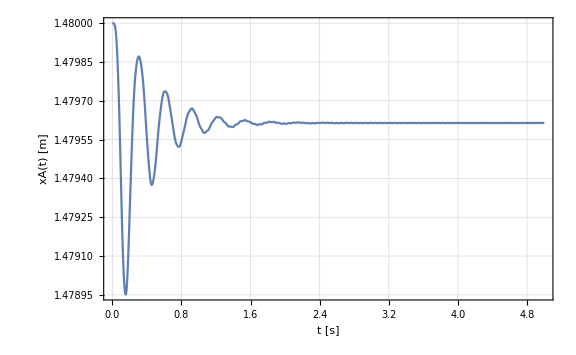

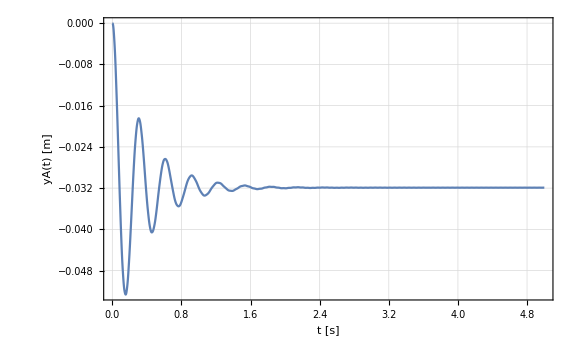

{1.47961,-0.0319095}

```mathematica
koti={ϕ1[t],ϕ2[t],ϕ3[t],ϕ4[t],ϕ5[t],ϕ6[t],ϕ7[t],ϕ8[t],ϕ9[t],ϕ10[t]};
koti=koti/.Resitev[[1]];
T1={0,0};
T2[t_]={L Cos[koti[[1]]],-L Sin[koti[[1]]]};
T3[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]};
T4[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]};
T5[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]]+L Cos[koti[[4]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]-L Sin[koti[[4]]]};
TA[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]]+L Cos[koti[[4]]]+L Cos[koti[[5]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]-L Sin[koti[[4]]]-L Sin[koti[[5]]]};
T7[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]]+L Cos[koti[[4]]]+L Cos[koti[[5]]]+L Cos[koti[[6]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]-L Sin[koti[[4]]]-L Sin[koti[[5]]]+L Sin[koti[[6]]]};
T8[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]]+L Cos[koti[[4]]]+L Cos[koti[[5]]]+L Cos[koti[[6]]]+L Cos[koti[[7]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]-L Sin[koti[[4]]]-L Sin[koti[[5]]]+L Sin[koti[[6]]]+L Sin[koti[[7]]]};
T9[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]]+L Cos[koti[[4]]]+L Cos[koti[[5]]]+L Cos[koti[[6]]]+L Cos[koti[[7]]]+L Cos[koti[[8]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]-L Sin[koti[[4]]]-L Sin[koti[[5]]]+L Sin[koti[[6]]]+L Sin[koti[[7]]]+L Sin[koti[[8]]]};
T10[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]]+L Cos[koti[[4]]]+L Cos[koti[[5]]]+L Cos[koti[[6]]]+L Cos[koti[[7]]]+L Cos[koti[[8]]]+L Cos[koti[[9]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]-L Sin[koti[[4]]]-L Sin[koti[[5]]]+L Sin[koti[[6]]]+L Sin[koti[[7]]]+L Sin[koti[[8]]]+L Sin[koti[[9]]]};
T11[t_]={L Cos[koti[[1]]]+L Cos[koti[[2]]]+L Cos[koti[[3]]]+L Cos[koti[[4]]]+L Cos[koti[[5]]]+L Cos[koti[[6]]]+L Cos[koti[[7]]]+L Cos[koti[[8]]]+L Cos[koti[[9]]]+L Cos[koti[[10]]],-L Sin[koti[[1]]]-L Sin[koti[[2]]]-L Sin[koti[[3]]]-L Sin[koti[[4]]]-L Sin[koti[[5]]]+L Sin[koti[[6]]]+L Sin[koti[[7]]]+L Sin[koti[[8]]]+L Sin[koti[[9]]]+L Sin[koti[[10]]]};

Plot[TA[t][[1]],{t,0,5},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","xA(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large]
Plot[TA[t][[2]],{t,0,5},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","yA(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large]

(*Export["Graf_10Ax.pdf",Plot[TA[t][[1]],{t,0,5},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","xA(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->450]]
Export["Graf_10Ay.pdf",Plot[TA[t][[2]],{t,0,5},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","yA(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->450]]

SystemOpen["Graf_10Ax.pdf"];
SystemOpen["Graf_10Ay.pdf"];*)
TA[5]
```